```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get["HopfE`"];
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={0->"S","S"+"I1"->2*"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2*"I2","S"+"Y2"->"Y2"+"I2","I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2*"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2*"Y1","Y1"->"R","R1"->"S","R2"->"S","R"->"S","S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};
rts={mu,be1*I1*S,be1*et1*Y1*S,ga1*I1,be2*I2*S,be2*et2*Y2*S,ga2*I2,be2*si2*I2*R1,be2*si2*et2*Y2*R1,ga2*Y2,be1*si1*I1*R2,be1*si1*et1*Y1*R2,ga1*Y1,th1*R1,th2*R2,th3*R,mu*S,mu*I1,mu*Y1,mu*R1,mu*I2,mu*Y2,mu*R2,mu*R};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAnalEx outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,E1,E2,EA,R0A,R12,R21,coP} = bdAnalEx[RN, rts];
{R01,R02}=R0A/.E0
p0val=par/.coP;
```

reactions and transitions: (0→S | mu
I1+S→2 I1 | be1 I1 S
S+Y1→I1+Y1 | be1 et1 S Y1
I1→R1 | ga1 I1
I2+S→2 I2 | be2 I2 S
S+Y2→I2+Y2 | be2 et2 S Y2
I2→R2 | ga2 I2
I2+R1→I2+Y2 | be2 I2 R1 si2
R1+Y2→2 Y2 | be2 et2 R1 si2 Y2
Y2→R | ga2 Y2
I1+R2→I1+Y1 | be1 I1 R2 si1
R2+Y1→2 Y1 | be1 et1 R2 si1 Y1
Y1→R | ga1 Y1
R1→S | R1 th1
R2→S | R2 th2
R→S | R th3
S→0 | mu S
I1→0 | I1 mu
Y1→0 | mu Y1
R1→0 | mu R1
I2→0 | I2 mu
Y2→0 | mu Y2
R2→0 | mu R2
R→0 | mu R)

RHS has var {S,I1,Y1,R1,I2,Y2,R2,R} par{be1,be2,et1,et2,ga1,ga2,mu,si1,si2,th1,th2,th3}

minimal siphons {{I1,Y1},{I2,Y2}} Check siphon={True,True}

Infection species  at positions: {2,3,5,6}

DFE solution E0: {R→0,R1→0,R2→0,S→1,I1→0,Y1→0,I2→0,Y2→0}

NGM K= ((be1 S)/(ga1+mu) | (be1 et1 S)/(ga1+mu) | 0 | 0
(be1 R2 si1)/(ga1+mu) | (be1 et1 R2 si1)/(ga1+mu) | 0 | 0
0 | 0 | (be2 S)/(ga2+mu) | (be2 et2 S)/(ga2+mu)
0 | 0 | (be2 R1 si2)/(ga2+mu) | (be2 et2 R1 si2)/(ga2+mu)) =((be1 S)/(ga1+mu) | (be1 et1 S)/(ga1+mu) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (be2 S)/(ga2+mu) | (be2 et2 S)/(ga2+mu)
0 | 0 | 0 | 0)

Reproduction functions R0A: {(be1 (S+et1 R2 si1))/(ga1+mu),(be2 (S+et2 R1 si2))/(ga2+mu)}

R0 at DFE: Max[(be1 S)/(ga1+mu),(be2 S)/(ga2+mu)]

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of boundary systems= 2 ;first sys has 3 sols, E1 is {S→(ga1+mu)/be1,I1→((be1-ga1-mu) (mu+th1))/(be1 (ga1+mu+th1)),Y1→0,R1→(ga1 (be1-ga1-mu))/(be1 (ga1+mu+th1)),R2→0,R→0} second sys has 3 sols, E2 is {S→(ga2+mu)/be2,R1→0,I2→((be2-ga2-mu) (mu+th2))/(be2 (ga2+mu+th2)),Y2→0,R2→(ga2 (be2-ga2-mu))/(be2 (ga2+mu+th2)),R→0}

under coP: {be1→4,be2→3,et1→1,et2→1,ga1→1,ga2→1,mu→1,si1→1,si2→1,th1→1/2,th2→1,th3→1} invasion nrs are{1.55556,1.05} repr nrs are{2.,1.5}

{be1/(ga1+mu),be2/(ga2+mu)}

```mathematica
p0val={1.5,1,1,1,1,1,0,25/10,3,1/10000,1/10000,1/10000};
plotInd={1,2};

ruSec=Thread[Delete[par,({#}&)/@plotInd]->Delete[p0val,({#}&)/@plotInd]];
Rl={R01,R02,R12,R21}/.ruSec;
Rl//Apart
cR=Thread[(Rl)>Table[11/10,{4}]];
(*Parameter values from the example*)
parBi=par[[plotInd]];
FindInstance[Join[Thread[parBi>0],cR],parBi]
```

{be1,be2,(25000 be1)/10001-(14999 be1)/(10001 be2),((-19999+30000 be1) be2)/(10001 be1)}

{{be1→2,be2→5/4}}

```mathematica
p0val={2,5/4,1,1,1,1,0,25/10,3,1/10000,1/10000,1/10000};
coP=Thread[par->p0val];

so=Solve[Thread[(RHS/.coP)==0],var]//N
so//Length
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},{I1→0.,Y1→0.,R1→0.0666667 (4.-5. S),I2→-0.0000333333 S,Y2→6.66667×10^-6 (-4.+5. S),R2→-0.333333 S,R→0.0666667 (-4.+5. S)},{I1→(S (12.-19. S+5. S^2))/(-300000.+975000. S),Y1→(6.66667×10^-6 (12.-43. S+43. S^2-10. S^3))/(-4.+13. S),R1→0.0666667 (4.-5. S),I2→(0.0000333333 (4. S-7. S^2-2. S^3))/(-4.+13. S),Y2→(6.66667×10^-6 (16.-48. S+27. S^2+10. S^3))/(-4.+13. S),R2→0.2 (1.-2. S),R→(0.466667 (4.-13. S+10. S^2))/(-4.+13. S)},{I1→-0.00004 S,Y1→0.00002 (-1.+2. S),R1→-0.4 S,I2→0.,Y2→0.,R2→0.2 (1.-2. S),R→0.2 (-1.+2. S)},{S→0.5,I1→0.0001 R1,Y1→0.,I2→0.,Y2→0.,R2→0.,R→0.},{S→0.8,I1→0.,Y1→0.,R1→0.,I2→0.0001 R2,Y2→0.,R→0.},{S→0.,I1→0.,Y1→-0.00002,R1→0.,I2→0.,Y2→0.,R2→0.2,R→-0.2},{S→0.,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},{S→0.,I1→0.,Y1→-0.00002,R1→0.266667,I2→0.,Y2→-0.0000266667,R2→0.2,R→-0.466667},{S→0.,I1→0.,Y1→0.,R1→0.266667,I2→0.,Y2→-0.0000266667,R2→0.,R→-0.266667},{S→0.307692,I1→0.,Y1→0.,R1→0.164103,I2→-0.0000102564,Y2→-0.0000164103,R2→-0.102564,R→-0.164103},{S→0.5,I1→0.,Y1→0.,R1→0.1,I2→-0.0000166667,Y2→-0.00001,R2→-0.166667,R→-0.1},{S→0.5,I1→0.00001,Y1→0.,R1→0.1,I2→0.,Y2→0.,R2→0.,R→0.}}

13

```mathematica
(*EXECUTE THIS FIRST:*)Clear[scan]

(*FindRoot-based equilibrium scanning with R-curve plotting*)
scan[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,steadyTol_:10^(-5),stabTol_:10^(-8),chopTol_:10^(-10),R01_:Automatic,R02_:Automatic,R12_:Automatic,R21_:Automatic]:=Block[{bifP1min,bifP1max,bifP2min,bifP2max,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,numpar,conPar,delta,wRan,hRan,eq,EE,E1,E2,DFE,eigs,complexEigs,realParts,jac,rCurves,fixedParams,fInd,activeEquations,activeColors,activeLabels,par1,par2,range1,range2},(*Set default step_size scanning parameters*)delta=1/10;
wRan=1;
hRan=1;
(*Fixed color mapping-keeping your colors*)colorMap=<|"DFE"->RGBColor[0,0,1],"E1"->RGBColor[0,1,0],"E2"->RGBColor[0.6,0.2,0.8],"EE-Stable"->RGBColor[1,1,0],"EE-Unstable"->RGBColor[0.9,0.4,0.4],"NoSol"->RGBColor[1,0,0]|>;
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
(*Parameters for R-curve plotting*)par1=par[[bifParIdx1]];
par2=par[[bifParIdx2]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Set parameter ranges and values*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
range1={bifP1min,bifP1max};
range2={bifP2min,bifP2max};
If[useGridMode,(*GRID MODE*)bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}]];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for scanning*)res={};
currentProgress=0;
progressVar=0;
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP-following exact logic from working version*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Solve equilibrium system with Total[var]==1 constraint like working version*)eq=Quiet[N[Solve[Join[Thread[(RHS/. conPar)==0],Thread[var>=0],{Total[var]==1}],var]],Solve::ratnz];
(*1. Try to find EE equilibrium first-exact logic from working version*)EE=Select[eq,(S/. #)>0&&(I1/. #)>0&&(I2/. #)>0&&(R1/. #)>0&&(R2/. #)>0&];
If[Length[EE]==1,(*Found EE-check stability like working version*)jac=D[RHS,{var}]/. conPar/. EE[[1]];
eigs=Chop[Eigenvalues[jac]//N,chopTol];
complexEigs=Select[eigs,Im[#]!=0&];
realParts=Re[complexEigs];
If[Length[complexEigs]>=2,If[Max[realParts]<0.,res=Append[res,{N[bifP1],N[bifP2],"EE-Stable"}];,res=Append[res,{N[bifP1],N[bifP2],"EE-Unstable"}];],res=Append[res,{N[bifP1],N[bifP2],"EE-Stable"}];];,(*2. Try to find E1 equilibrium-exact logic from working version*)E1=Select[eq,(S/. #)>0&&(I1/. #)>0&&(R1/. #)>0&];
If[Length[E1]==1,res=Append[res,{N[bifP1],N[bifP2],"E1"}];,(*3. Try to find E2 equilibrium-exact logic from working version*)E2=Select[eq,(S/. #)>0&&(I2/. #)>0&&(R2/. #)>0&];
If[Length[E2]==1,res=Append[res,{N[bifP1],N[bifP2],"E2"}];,(*4. Try to find DFE equilibrium-exact logic from working version*)DFE=Select[eq,(S/. #)>0&];
If[Length[DFE]>=1,res=Append[res,{N[bifP1],N[bifP2],"DFE"}];,(*No solution found*)res=Append[res,{N[bifP1],N[bifP2],"NoSol"}];];];];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create plot with fixed colors*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
plotMarkers=Table[{Style["■",colorMap[outcomes[[i]]]],12},{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->plotMarkers,PlotLegends->outcomes,AspectRatio->1,PlotRange->{range1,range2},GridLines->Automatic];
(*Create R-curve plots*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R12=!=Automatic||R21=!=Automatic,(*Create fixed parameter substitution rules*)fInd=Complement[Range[Length[par]],plotInd];
fixedParams=Thread[par[[fInd]]->p0val[[fInd]]];
(*Define R curves,colors,and labels*)activeEquations={};
activeColors={};
activeLabels={};
If[R01=!=Automatic,AppendTo[activeEquations,Evaluate[(R01/. fixedParams)==1]];
AppendTo[activeColors,Directive[Red,Thick]];
AppendTo[activeLabels,Style["R01 = 1",Red]];];
If[R02=!=Automatic,AppendTo[activeEquations,Evaluate[(R02/. fixedParams)==1]];
AppendTo[activeColors,Directive[Blue,Thick]];
AppendTo[activeLabels,Style["R02 = 1",Blue]];];
If[R12=!=Automatic,AppendTo[activeEquations,Evaluate[(R12/. fixedParams)==1]];
AppendTo[activeColors,Directive[Purple,Thick]];
AppendTo[activeLabels,Style["R12 = 1",Purple]];];
If[R21=!=Automatic,AppendTo[activeEquations,Evaluate[(R21/. fixedParams)==1]];
AppendTo[activeColors,Directive[Green,Thick]];
AppendTo[activeLabels,Style["R21 = 1",Green]];];
(*Create ContourPlot with all R-curves*)If[Length[activeEquations]>0,rCurves={ContourPlot[Evaluate[activeEquations],Evaluate[{par1,range1[[1]],range1[[2]]}],Evaluate[{par2,range2[[1]],range2[[2]]}],ContourStyle->activeColors,PlotPoints->50]};];];
(*Combine plots*)If[Length[rCurves]>0,finalPlot=Show[finalPlot,rCurves[[1]],Frame->True,FrameLabel->{ToString[par1],ToString[par2]},PlotLabel->"Equilibrium Classification with R-curves",ImageSize->450];,finalPlot=Show[finalPlot,Frame->True,FrameLabel->{ToString[par1],ToString[par2]},PlotLabel->"Equilibrium Classification",ImageSize->450];];
(*Simple summary with percentages*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NoSol points as errors*)noSolPoints=Select[res,#[[3]]=="NoSol"&];
{finalPlot,noSolPoints,res}];

(*Andras,I added these variables for the following reasons:-stabTol,chopTol: function parameters for easy adjustment of numerical precision-rCurves,fixedParams,fInd,activeEquations,activeColors,activeLabels:for R-curve plotting functionality-par1,par2,range1,range2:for cleaner R-curve plotting parameter handling-colorMap:for consistent color mapping across different equilibrium types-useGridMode:handles both grid mode (scan[RHS,var,par,p0val,plotInd,gridRes->30]) and range scanning modes (scan[RHS,var,par,p0val,plotInd]  (*or gridRes->Automatic*); to speed up this, inrease delta, hardcoded on first line)*)
```

DFE: 100 (10%)

E2: 105 (10%)

EE-Unstable: 379 (38%)

E1: 171 (17%)

EE-Stable: 245 (24%)

{80.125,Null}

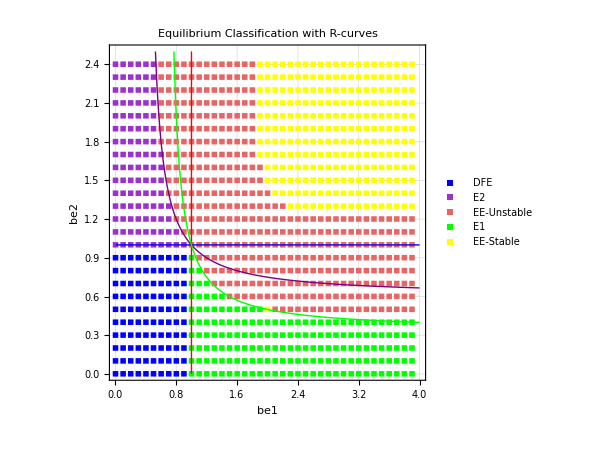

```mathematica
steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```

```mathematica
Export["partitionScan.pdf",fPl]
```

partitionScan.pdf